## CSE 477 Introduction to Computer-aided Geometric Design Instructor: Dianne Hansford Homework #0: Getting Started with MM Optional -- Does not count toward your grade

#### Description : In this homework, you will demonstrate knowledge of the basics of MM. Use the tutorial nb as a guide and do not hesitate to use the Help. Follow the instructions in each cell below. Use Shift-Enter to execute each cell as you work on it.

Part 1: Create a new cell below this one using format style Subsection.
In this new cell, write your name.

Jesus Canez

Part 2: Modify the code in the next cell so that when executed, the value of variable var1 is printed (not suppressed).

```mathematica
var1 = 2
var2 = 3;
```

2

Part 3: Add an in-line comment to the cell below, describing what is being done in the cell.

```mathematica
(* three variables are being defined a, b, and c. c has the value of a + b *)
a = 3;
b = 4;
c = a + b;
```

Part 4: Add a print statement to the cell below. The print statement must have three elements: the text describing the variable, the variable name, and the variable value.

```mathematica
myvar = Sum[i,{i,1,10}];
Print["This is the result of adding 1 through 10 together and saved into myvar = ", myvar];
```

This is the result of adding 1 through 10 together and saved into myvar = 55

Part 5: Create a plot of the cosine function between -Pi and Pi.

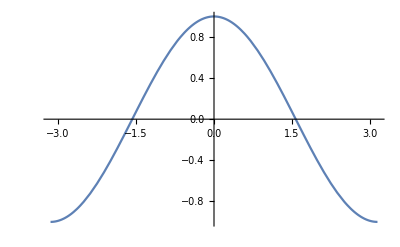

```mathematica
cosPlot = Plot[Cos[x], {x, -Pi, Pi}]
```

Part 6: Create a plot of the cosine function between -Pi and Pi and add the plotting option that preserves the actual coordinate values in the plot. (This will eliminate the distortion in the previous plot.)

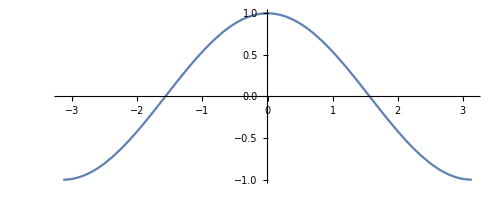

```mathematica
Plot[Cos[x], {x, -Pi, Pi}, AspectRatio->Automatic]
```

Part 7: Create a Manipulate environment that modifies the amplitude of the plot of the cosine function from Part 5 to vary between 1.0 and 2.0.
See https://www.mathsisfun.com/algebra/amplitude-period-frequency-phase-shift.html for a picture of amplitude.

```mathematica
Manipulate[Plot[c * Cos[x ], {x, -Pi, Pi}], {{c, 1, "Amplitude"}, 1.0, 2.0}]
```

Part 8: Correct the code below.

```mathematica
p = RandomReal[{-2,-1}];
q = Abs[p] + Abs[2];
result = p + q
```

2.

Part 9: Create a function called hwfct with integer input variable “input” and outputs the square of the input. The function should have two lines of code and use the Return statement.
Call the function for input=2 and use a print statement to output the functions value. All other output should be suppressed.

```mathematica
hwfct[input_] := (
thisResult = input^2;
Return[thisResult];
);
input2 = hwfct[2];
Print[input2];
```

4

Part 10: Using Table, create the set of {x,y} integer pairs {1,5}, {2,6}, {3,7}. Using a print statement, print the table in its normal form and formatted using MatrixForm. Include text in the print statement.
In a second print statement, print (2,6) by accessing the table variable.
In a third print statement, print the 6 value by accessing the table variable.

```mathematica
myNewTable = Table[{i, i+4},{i, 1, 3} ];
Print[MatrixForm[myNewTable]];
Print[myNewTable[[2]]];
Print[myNewTable[[2,2]]];
```

(1 | 5
2 | 6
3 | 7)

{2,6}

6

Part 11: Create a Do loop that sums the integers from 1 to 100. Before the Do statement, initialize the summation variable. Print the result.

```mathematica
myit = 1;
mySum = 0;
tempHolder = 0;
Do[(
mySum = myit + tempHolder;
tempHolder = mySum;), 
{myit, 1, 100}
];
Print[mySum];
```

5050